Mathematica notebook file is available upon request (Jae Kyoung Kim, KAIST, jaekkim@kaist.ac.kr)

```mathematica
endt=300; (*Simulation time*)

(*Parameters. See Table S3 for details*)
{ao,at, kpf,kcf, kppf,Kd,Kcbo,Kcbt,Kcbh,Kppb,kpo,kr1,kr2,kp,kppo,kpp,CKt1,CKt2,PPt,ACt,do,bo,bt,bh,ub}={59.5, 1, 0.032,10.77,7.32,1.555*10^-5,6.05,1.7,5.22*10^-14,0.0694,287.5, 6.6, 38.8, 0.61, 28.166, 9.608, 166.1, 203, 11.504, 1.366, 0.242, 6.77*10^-4, 73.157, 0.339,655.9};

(*Model equations. See Table S1 and S2 for details*)
aone=
{m'[t]==ao*(1-(c4[t]+c4PP[t]+c4CK1[t]+c4CK2[t])/ACt-Kd/ACt+Sqrt[(1-(c4[t]+c4PP[t]+c4CK1[t]+c4CK2[t])/ACt-Kd/ACt)^2+4*Kd/ACt])/2-do*m[t],
c0'[t]==at*m[t]-kpf*c0[t]*(CK1[t]+CK2[t])+Kcbo*c0CK1[t]+Kcbo*c0CK2[t]+kpp*c1PP[t]+kppo*ct1PP[t]-bo*c0[t],
c0CK1'[t]==kpf*c0[t]*CK1[t]-(Kcbo+kr1+bo+kpo)*c0CK1[t],c0CK2'[t]==kpf*c0[t]*CK2[t]-(Kcbo+kr2+bo+kpo)*c0CK2[t],
ct1'[t]==kpo*c0CK1[t]+kpo*c0CK2[t]-kppf*ct1[t]*PP[t]+Kppb*ct1PP[t]-(ub+bo)*ct1[t],
ct1PP'[t]==kppf*ct1[t]*PP[t]-(Kppb+ub+bo+kppo)*ct1PP[t],
c1'[t]==kr1*c0CK1[t]+kr2*c0CK2[t]-kppf*c1[t]*PP[t]+Kppb*c1PP[t]-kcf*c1[t]*(CK1[t]+CK2[t])+Kcbt*c1CK1[t]+Kcbt*c1CK2[t]-bo*c1[t]+kpp*c2PP[t],
c1PP'[t]==kppf*c1[t]*PP[t]-(Kppb+bo+kpp)*c1PP[t],
c1CK1'[t]==kcf*c1[t]*CK1[t]-(Kcbt+kp+bo)*c1CK1[t],
c1CK2'[t]==kcf*c1[t]*CK2[t]-(Kcbt+kp+bo)*c1CK2[t],
c2'[t]==kp*(c1CK1[t]+c1CK2[t])-kppf*c2[t]*PP[t]+Kppb*c2PP[t]-kcf*c2[t]*(CK1[t]+CK2[t])+Kcbt*c2CK1[t]+Kcbt*c2CK2[t]-bo*c2[t]+kpp*c3PP[t],
c2PP'[t]==kppf*c2[t]*PP[t]-(Kppb+bo+kpp)*c2PP[t],
c2CK1'[t]==kcf*c2[t]*CK1[t]-(Kcbt+kp+bo)*c2CK1[t],
c2CK2'[t]==kcf*c2[t]*CK2[t]-(Kcbt+kp+bo)*c2CK2[t],
c3'[t]==kp*(c2CK1[t]+c2CK2[t])-kppf*c3[t]*PP[t]+Kppb*c3PP[t]-kcf*c3[t]*(CK1[t]+CK2[t])+Kcbh*c3CK1[t]+Kcbh*c3CK2[t]-bo*c3[t]+kpp*c4PP[t],
c3PP'[t]==kppf*c3[t]*PP[t]-(Kppb+bo+kpp)*c3PP[t],
c3CK1'[t]==kcf*c3[t]*(CK1[t])-(Kcbh+kp+bo)*c3CK1[t],
c3CK2'[t]==kcf*c3[t]*(CK2[t])-(Kcbh+kp+bo)*c3CK2[t],
c4'[t]==kp*(c3CK1[t]+c3CK2[t])-kppf*c4[t]*PP[t]+Kppb*c4PP[t]-kcf*c4[t]*(CK1[t]+CK2[t])+Kcbh*c4CK1[t]+Kcbh*c4CK2[t]-bh*c4[t],
c4PP'[t]==kppf*c4[t]*PP[t]-(Kppb+bh+kpp)*c4PP[t],
c4CK1'[t]==kcf*c4[t]*CK1[t]-(Kcbh+bh)*c4CK1[t],
c4CK2'[t]==kcf*c4[t]*CK2[t]-(Kcbh+bh)*c4CK2[t],
cub'[t]==ub*(ct1[t]+ct1PP[t])-bt*cub[t],
CK1'[t]==-kcf*CK1[t]*(c1[t]+c2[t]+c3[t]+c4[t])-kpf*c0[t]*CK1[t]+(kp+bo)*(c1CK1[t]+c2CK1[t]+c3CK1[t])+bh*c4CK1[t]+(Kcbo+kr1+bo+kpo)*(c0CK1[t])+Kcbt*(c1CK1[t]+c2CK1[t])+Kcbh*(c3CK1[t]+c4CK1[t]),CK2'[t]==-kcf*CK2[t]*(c1[t]+c2[t]+c3[t]+c4[t])-kpf*c0[t]*CK2[t]+(kp+bo)*(c1CK2[t]+c2CK2[t]+c3CK2[t])+bh*c4CK2[t]+(Kcbo+kr2+bo+kpo)*(c0CK2[t])+Kcbt*(c1CK2[t]+c2CK2[t])+Kcbh*(c3CK2[t]+c4CK2[t]),PP'[t]==-kppf*PP[t]*(ct1[t]+c1[t]+c2[t]+c3[t]+c4[t])+(Kppb+kpp+bo)*(c1PP[t]+c2PP[t]+c3PP[t])+(Kppb+kppo+bo)*ct1PP[t]+(Kppb+kpp+bh)*c4PP[t]+ub*ct1PP[t]};
atwo={m[0]==0,c0[0]==0,c0CK1[0]==0,c0CK2[0]==0,ct1[0]==0,ct1PP[0]==0,c1[0]==0,c1PP[0]==0,c1CK1[0]==0,c1CK2[0]==0,c2[0]==0,c2PP[0]==0,c2CK1[0]==0,c2CK2[0]==0,c3[0]==0,c3PP[0]==0,c3CK1[0]==0,c3CK2[0]==0,c4[0]==0,c4PP[0]==0,c4CK1[0]==0,c4CK2[0]==0,cub[0]==0,CK1[0]==CKt1,CK2[0]==CKt2,PP[0]==PPt};
afive={m,c0,c0CK1,c0CK2,ct1,ct1PP,c1,c1PP,c1CK1,c1CK2,c2,c2PP,c2CK1,c2CK2,c3,c3PP,c3CK1,c3CK2,c4,c4PP,c4CK1,c4CK2,cub,CK1,CK2,PP};
qt=NDSolve[Join[aone,atwo],afive,{t,0,endt},MaxSteps->10000000,MaxStepSize->0.01];
```

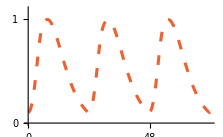

```mathematica
(*Simulated PER trajectory*)

k[t_]:=c0[t]+c0CK1[t]+c0CK2[t]+ct1[t]+ct1PP[t]+c1[t]+c1PP[t]+c1CK1[t]+c1CK2[t]+c2[t]+c2PP[t]+c2CK1[t]+c2CK2[t]+c3[t]+c3PP[t]+c3CK1[t]+c3CK2[t]+c4[t]+c4PP[t]+c4CK1[t]+c4CK2[t]+cub[t] ;

xqt=qt;
po=FindPeaks[Table[-k[t]/.xqt[[1]],{t,0,endt,0.1}]][[3]][[1]];
wX=Table[k[t]/.xqt[[1]],{t,po*0.1,po*0.1+24*3,0.1}];
wX=wX/Max[wX];
ytick={0,23/2,23}/23;
ytickl={0,"",1};
xtick={0,3,6,9,12,15,18,21,24}*40;
xtickl={0,"",24,"",48,"",72,"",24};
is=72 1.55*3/1.5;
ta=0.006/2;(*Thickness of axis*)
ts=0.02; (*length of thick*)
ft=15;
top=1.1;
ListLinePlot[{wX},Ticks->{Table[{xtick[[jj]],xtickl[[jj]],{0,ts}},{jj,1,Length[xtick]}],Table[{ytick[[jj]],ytickl[[jj]],{0,ts}},{jj,1,Length[ytick]}]},AxesStyle->Directive[Thickness[ta],FontSize->ft,Black],PlotRange->{0,top},ImageSize->is,PlotStyle->Join[{{ColorData[97,"ColorList"][[4]],AbsoluteDashing[{7,
10}],Thickness[0.01]}}, Table[ColorData[97,"ColorList"][[j]],{j,{3,2,1}}]],PlotStyle-> Table[ColorData[97,"ColorList"][[j]],{j,{4,2,3,1}}]]
```